```mathematica
Quit[]
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/cesarecarlomella/Desktop/Physics/Oxford/projects/correlator/2loop

```mathematica
<<LiteRed2`
<<Mint`
```

**************** LiteRed v2.025β ********************
Author: Roman N. Lee, Budker Institute of Nuclear Physics, Novosibirsk.
Release Date: ????-??-??
Timestamp: Tue 1 Apr 2025 22:18:26
Read from:/Users/cesarecarlomella/Software/LiteRed2/LiteRed2025.m (CRC32:2902354241,{2340977437, 3317197336, 1063727846})

LiteRed stands for Loop integrals Reduction.
The package is designed for the search and application of the Integration-By-Part reduction rules. It also contains some other useful tools.

See ?LiteRed`* for a list of functions.

Get::noopen: Cannot open Mint`.

$Failed

```mathematica
convert=Table[ToExpression["topo"<>ToString[i]]-> ToExpression["IF"<>ToString[i]], {i,1,2}];
intfamvoc=Table[ToExpression["IF"<>ToString[i]],{i,1,2}];
```

## Integral family definition topo1

```mathematica
family = topo1;
```

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m2},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m2, sp[k2,k2]-m2, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m2,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m2,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m2}
```

{-m2+k1·k1,-m2+k2·k2,-m2+k1·k1+2 k1·k2+k2·k2,-m2+pp+k1·k1-2 k1·p,-m2+pp+k2·k2+2 k2·p}

```mathematica
(*(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[family,intfam,{k1,k2},Directory->"topo1"]

GenerateIBP[family];

AnalyzeSectors[family];

FindSymmetries[family];

(*Solve IBP reduction for unique sectors*)
(*--------------------------------------------------------------*)
SolvejSector/@UniqueSectors[family];

(*Save to disk*)
DiskSave[family];*)
```

```mathematica
intfam//TableForm
```

-m2+k1·k1
-m2+k2·k2
-m2+k1·k1+2 k1·k2+k2·k2
-m2+pp+k1·k1-2 k1·p
-m2+pp+k2·k2+2 k2·p

```mathematica
FromDigits[{1,1,1,1,1},2]
```

31

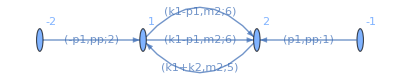

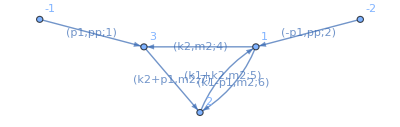

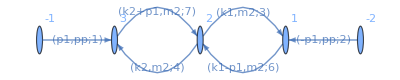

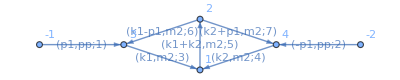

```mathematica
(*Import["./graphs/topo1/all/topo1_2_24.dot"]
Import["./graphs/topo1/all/topo1_3_28.dot"]
Import["./graphs/topo1/all/topo1_3_26.dot"]*)
Import["./graphs/topo1/all/topo1_3_14.dot"]
Import["./graphs/topo1/all/topo1_4_30.dot"]
Import["./graphs/topo1/all/topo1_4_27.dot"]
Import["./graphs/topo1/all/topo1_5_31.dot"]
```

```mathematica
Get["./topo1/topo1"];
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
MIs[family]
mis=MIs[family];
tomis=ToMIsRule[mis];
(*Put[mis,"./Reduction/FamRed/"<>ToString[family]<>"/"<>"Mi"]
MIs[family];*)
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*LiteRed Masters*)
todiff= MIs[family];
```

```mathematica
(*diff eq for LiteRed Masters*)
derpp = Dinv[todiff,pp];
derm2 = Dinv[todiff,m2];
rhs=Union[Join[Union@Cases[derpp, j[family,a__],Infinity],Union@Cases[derm2, j[family,a__],Infinity]]];
rhsRed = Collect[IBPReduce[rhs],{_j}, Factor];
ReplaceRHS = Thread[Rule[rhs,rhsRed]];
redderpp=Collect[derpp/.ReplaceRHS, {_j},Factor];
redderm2=Collect[derm2/.ReplaceRHS, {_j},Factor];
MppLiteRed = CoefficientArrays[redderpp,todiff][[2]]//Normal;
Mm2LiteRed = CoefficientArrays[redderm2,todiff][[2]]//Normal;
```

```mathematica
MIs[family]
```

{j[topo1,0,0,0,1,1],j[topo1,0,0,1,1,1],j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,2,1,1,0],j[topo1,0,1,1,1,1],j[topo1,1,1,0,1,1],j[topo1,1,1,1,1,1]}

```mathematica
(*(*My Masters*)
mybasis= {  j[topo1,0,0,0,2,2],
j[topo1,0,0,1,1,2],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,2,0,2,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
j[topo1,0,2,1,1,0],
j[topo1,0,1,1,1,1],
j[topo1,1,1,0,1,1],
j[topo1,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mpp=(D[R.T,pp].Inverse[R.T]//Simplify) + R.T.MppLiteRed.(Inverse[R.T])//PowerExpand//Simplify;
Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;*)
(*Integrate[Mu[[;;2]]/.d-> 4,u]
Integrate[Mz[[;;2]]  /.d-> 4,z]*)
```

```mathematica
(*My Masters basis in d=2*)
mybasis= {  j[topo1,0,0,0,1,1],
m2 j[topo1,0,0,1,1,1],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,1,0,1,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],m2],
 m2 √(pp (4 m2-pp))j[topo1,0,1,1,1,1],
(pp-4 m2)j[topo1,1,1,0,1,1],
pp j[topo1,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mpp=(D[R.T,pp].Inverse[R.T]//Simplify) + R.T.MppLiteRed.(Inverse[R.T])//PowerExpand//Simplify;
Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;
```

{j[topo1,0,0,0,1,1],m2 j[topo1,0,0,1,1,1],√(4 m2-pp) √pp j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,1,1,2,0]+j[topo1,0,1,2,1,0]+j[topo1,0,2,1,1,0],m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1],(-4 m2+pp) j[topo1,1,1,0,1,1],pp j[topo1,1,1,1,1,1]}

```mathematica
Mm2 // MatrixForm
```

((-2+d)/m2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | (-2+d)/m2 | 0 | 0 | 0 | 0 | 0 | 0
-((-2+d) √pp)/(m2 √(4 m2-pp)) | 0 | ((-2+d) (8 m2-pp))/(2 m2 (4 m2-pp)) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
(3 (-2+d)^2 pp)/(2 m2^2 (m2-pp) (9 m2-pp)) | 0 | 0 | -(3 (-3+d) (-8+3 d) (3 m2-pp))/(2 m2 (m2-pp) (9 m2-pp)) | (9 (-16+5 d) m2^2+10 (10-3 d) m2 pp+(-4+d) pp^2)/(2 m2 (m2-pp) (9 m2-pp)) | 0 | 0 | 0
0 | -((-2+d) √pp)/(2 m2 √(4 m2-pp)) | 0 | ((-8+3 d) √pp)/(2 √(4 m2-pp)) | -(5 m2 √pp)/(3 √(4 m2-pp)) | ((-2+d) (8 m2-pp))/(2 m2 (4 m2-pp)) | 0 | 0
0 | 0 | (2 (-2+d))/(m2 √(4 m2-pp) √pp) | 0 | 0 | 0 | (4 (-2+d))/(4 m2-pp) | 0
0 | ((-2+d) pp)/(m2^2 (12 m2^2-7 m2 pp+pp^2)) | ((-2+d) (2 m2-pp) √pp)/(m2^2 (3 m2-pp) (4 m2-pp)^(3/2)) | ((8-3 d) pp)/(m2 (12 m2^2-7 m2 pp+pp^2)) | (2 pp (m2+pp))/(3 m2 (3 m2-pp) (4 m2-pp)) | -(4 (-3+d) √pp)/(m2 (3 m2-pp) (4 m2-pp)^(3/2)) | -((-3+d) pp^2)/(m2 (3 m2-pp) (-4 m2+pp)^2) | ((-4+d) (6 m2-pp))/(2 m2 (3 m2-pp)))

#### Elliptic Sector

```mathematica
(*(*My Masters*)
mybasis= {  j[topo1,0,0,0,2,2],
j[topo1,0,0,1,1,2],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,2,0,2,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],m2],
j[topo1,0,1,1,1,1],
j[topo1,1,1,0,1,1],
j[topo1,1,1,1,1,1]}
(* my = T.LiteRed*)
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
R = IdentityMatrix[8];
Mpp=(D[R.T,pp].Inverse[R.T]//Simplify) + R.T.MppLiteRed.(Inverse[R.T])//PowerExpand//Simplify;
Mm2=(D[R.T,m2].Inverse[R.T]//Simplify) + R.T.Mm2LiteRed.(Inverse[R.T])//PowerExpand//Simplify;
(*Integrate[Mu[[;;2]]/.d-> 4,u]
Integrate[Mz[[;;2]]  /.d-> 4,z]*)*)
```

```mathematica
Mpp[[4;;5,4;;5]]//MatrixForm
Mm2[[4;;5,4;;5]]//MatrixForm
```

((-3+d)/pp | -m2/pp
(3 (-3+d) (-8+3 d) (3 m2-pp))/(2 (m2-pp) (9 m2-pp) pp) | (-9 (-8+3 d) m2^2+10 (-2+d) m2 pp+(-4+d) pp^2)/(2 pp (-9 m2+pp) (-m2+pp)))

(0 | 1
-(3 (-3+d) (-8+3 d) (3 m2-pp))/(2 m2 (m2-pp) (9 m2-pp)) | (9 (-16+5 d) m2^2+10 (10-3 d) m2 pp+(-4+d) pp^2)/(2 m2 (m2-pp) (9 m2-pp)))

```mathematica
Mm2[[4;;5,4;;5]]/.d -> 2 -2 eps//MatrixForm  // Simplify
```

(0 | 1
-(3 (1+2 eps) (1+3 eps) (3 m2-pp))/(m2 (m2-pp) (9 m2-pp)) | (-9 (3+5 eps) m2^2+10 (2+3 eps) m2 pp-(1+eps) pp^2)/(m2 (m2-pp) (9 m2-pp)))

```mathematica
(* 

picard Fuchs operator in d = 2 dimesnions 

*)
(Mm2[[5,4;;5]] /. d-> 2// Together)
pf=d2MI-% .{MI, d1MI}/. pp -> 1
PF=pf  /. {  d1MI -> 1/m2 θ, d2MI -> 1/m2^2(θ^2-θ)} /.MI -> 1 /. m2 -> λ
```

{-(3 (3 m2-pp))/(m2 (m2-pp) (9 m2-pp)),(-27 m2^2+20 m2 pp-pp^2)/(m2 (m2-pp) (9 m2-pp))}

d2MI-(d1MI (-1+20 m2-27 m2^2))/((-1+m2) m2 (-1+9 m2))+(3 (-1+3 m2) MI)/((-1+m2) m2 (-1+9 m2))

(-θ+θ^2)/λ^2+(3 (-1+3 λ))/((-1+λ) λ (-1+9 λ))-(θ (-1+20 λ-27 λ^2))/((-1+λ) λ^2 (-1+9 λ))

```mathematica
(* combine string of operators. F1 will be in the operator, F2 in the ansatz *)
combineOperator = { F1[a__]F2[b__] :> F[a,b], F1[a__]-> F[a] , F2[a__] -> F[a] };
(* move the θ operator to the right for polynomial and logs *)
moveRightPoly = {F[a___,θ, g[ρ,m_],b___]->  m F[a,g[ρ,m],b]  + F[a,g[ρ,m], θ,b]};
moveRightLog = {F[a___,θ, g[log,1],b___]->  F[a,b]  + F[a,g[log,1], θ,b]};
(* extract from the functions the logs and the polynomial *)
extractPoly = { F[g[ρ,m_],b___] -> ρ^m F[b], F[g[log,1],g[ρ,m_],b___] -> ρ^m log F[b] };
extractPolySol = { F2[g[ρ,m_]] -> ρ^m , F2[g[log,n_],g[ρ,m_]] -> ρ^m L^n };
(* Once the operator is completely to the right, it annihilates nothing *)
zeroOP = {F[θ]->0,F[θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ]->0,F[θ,θ,θ,θ]->0,F[θ,θ,θ,θ,θ]->0};
SolveForAnsatzMUM[point_, maxorder_, indicial_, operator_] := Module[{ansatz, sol0, sol1,coeffSol,der,derpoly,derpolyLog,tmp},
(*first solution*)
ansatz = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}];
(*boundary*)
coeffSol={a[0]-> 1};
(* Apply operator to ansatz *)
der=Expand[operator ansatz] //. combineOperator  //.moveRightPoly //.extractPoly /. F[]->1  /. zeroOP;
Do[
tmp=Flatten[Solve[(Coefficient[der,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol0 = Sum[a[n]F2[g[ρ,n+indicial]], {n,0,maxorder}] /. coeffSol;
Clear[ansatz];
(*second solution*)
ansatz =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}];
(*boundary*)
der=Expand[operator ansatz] //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP;
derpoly=Coefficient[der,log,0];
derpolyLog=Coefficient[der,log,1];
Do[
tmp=Flatten[Solve[(Coefficient[derpoly,ρ,i+indicial]/.coeffSol) ==0]];
coeffSol = Join[coeffSol,tmp], {i,1,maxorder}];
sol1 =Sum[a[n] F2[g[log,1], g[ρ,n+indicial]], {n,0,maxorder}]+ Sum[b[n]F2[g[ρ,n+indicial]], {n,1,maxorder}]/. coeffSol;
Return[{sol0,sol1, coeffSol}];
]
```

```mathematica
(* this is the derivative operator in lambada = m2 *)
OP =Collect[(-  Collect[λ^2 (1-9 λ)(λ-1)  PF , {θ},Together] /.{ θ θ-> F[θ,θ] ,  θ-> F[θ]}  //Expand) , _F, Factor]
```

3 λ (-1+3 λ)+2 λ (-5+9 λ) F[θ]+(-1+λ) (-1+9 λ) F[θ,θ]

```mathematica
(* generically, if we want to shift λ = λ0 + ρ and expand around ρ ~ 0 (λ ~ λ0), the transformation is the following *)
OPlambda0 =Collect[ Collect[OP   /. {F[θ] -> F[θ] (1 + λ0/ρ) ,F[θ,θ] ->((λ0+ρ) (-λ0 F[θ]+(λ0+ρ) F[θ,θ]))/ρ^2, λ  -> λ0 +ρ }, {_F}, Simplify], {_F} ,Simplify];
(* choose here a point *)
toapply=(OPlambda0/. λ0 ->0/. F -> F1)//Expand
(* indicial equation*)
Print["indicial equation:  ",( toapply /. ρ ->  0) == 0 ]
(* indices 0 *)
```

-3 ρ+9 ρ^2-10 ρ F1[θ]+18 ρ^2 F1[θ]+F1[θ,θ]-10 ρ F1[θ,θ]+9 ρ^2 F1[θ,θ]

indicial equation:  F1[θ,θ]==0

```mathematica
(* Solution around MUM point

 *)
point  = 0;
maxorder =22;
indicial= 0;
{sol[point][0],sol[point][1], coeffSol[point]}=SolveForAnsatzMUM[point,maxorder,indicial,toapply];
```

```mathematica
(* check the solution up to the requested order *)
(Series[Expand[toapply sol[point][0]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP, {ρ,0,maxorder}]//Normal) /. ρ^(a_)/; a> 99 :> 0
(Series[Expand[toapply sol[point][1]]  //. combineOperator  //.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP//Expand, {ρ,0,maxorder}]//Normal)/. ρ^(a_)/; a> 99 :> 0
```

0

0

```mathematica
(* Griffiths transversality condition (don't remember where they come from) *)
Σ = {{0,1},{-1,0}}
(*this is obvious*)
(*Print[{ω0,ω1}.Σ.{ω0,ω1}]*)
griff=Collect[Series[{ω0,ω1}.Σ.{dω0,dω1}   /. {ω0 -> (sol[point][0] /. extractPolySol),ω1 -> (sol[point][1] /. extractPolySol),dω0->  D[((sol[point][0]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP/. log -> L) ,ρ],dω1-> D[((sol[point][1]//Expand) //.combineOperator//.moveRightLog //. moveRightPoly//.extractPoly /. F[]->1  /. zeroOP /. log -> L)/.L-> Log[ρ],ρ] /. Log[ρ]->L} ,{ ρ, 0,10}]//Normal, {ρ}, Together];
Series[(n[0]+n[1]ρ + n[2]ρ^2 + n[3] ρ^3)/(ρ(-1+ρ) (-1+9 ρ)), {ρ,0,10}] //Expand //Normal ;
Collect[%, {ρ}] /. {n[0] -> 1, n[1] -> 0, n[2] -> 0, n[3]->0};
Print["check the transversality condition:  ",griff-%]
gtc=(n[0]+n[1]ρ + n[2]ρ^2)/(ρ(-1+ρ) (-1+9 ρ))/. {n[0] -> 1, n[1] -> 0, n[2] -> 0, n[3]-> 0}//Simplify//Factor
{ω0,ω1}.Σ.{dω0,dω1}==gtc
repl=Solve[% /. dω0 ω1 -> V  ,V] /. V -> dω0 ω1  //Flatten
```

{{0,1},{-1,0}}

check the transversality condition:  0

1/((-1+ρ) ρ (-1+9 ρ))

dω1 ω0-dω0 ω1==1/((-1+ρ) ρ (-1+9 ρ))

{dω0 ω1→-1/((-1+ρ) ρ (-1+9 ρ))+dω1 ω0}

```mathematica
(* Split the matrix {{ω0,ω1},{dω0,dω1}} into Unipotent and Semi-Simple *)
Wu = {{1,  ω1/ω0},{0,1}}
Wss = {{ω0,0},{dω0,gtc/ω0}}
Wss.Wu /. repl//Simplify
```

{{1,ω1/ω0},{0,1}}

{{ω0,0},{dω0,1/((-1+ρ) ρ (-1+9 ρ) ω0)}}

{{ω0,ω1},{dω0,dω1}}

```mathematica
InvWss=Inverse[Wss]//Simplify
```

{{1/ω0,0},{-dω0 (-1+ρ) ρ (-1+9 ρ),(-1+ρ) ρ (-1+9 ρ) ω0}}

```mathematica
Wss//MatrixForm
```

(ω0 | 0
dω0 | 1/((-1+ρ) ρ (-1+9 ρ) ω0))

```mathematica
Print["new basis is J,  I = Wss J"]
```

new basis is J,  I = Wss J

```mathematica
(*(Solve[(pf /. m2 -> λ /. λ ->  ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten)*)
```

```mathematica
(Solve[(pf /. m2 -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify
```

{d2ω0→-(dω0-20 dω0 ρ+27 dω0 ρ^2-3 ω0+9 ρ ω0)/(ρ-10 ρ^2+9 ρ^3)}

```mathematica
derinvWss=D[InvWss,ρ]  +(InvWss /. dω0 -> d2ω0  /. 1/ω0 ->( -1/uω0^2 )dω0 /. ω0-> dω0  /. uω0 -> ω0 ) /.((Solve[(pf /. m2 -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify)//Simplify
```

{{-dω0/ω0^2,0},{3 (-1+3 ρ) ω0,dω0 ρ (1-10 ρ+9 ρ^2)+(1-20 ρ+27 ρ^2) ω0}}

```mathematica
derinvWss.Wss//MatrixForm
```

(-dω0/ω0 | 0
3 (-1+3 ρ) ω0^2+dω0 (dω0 ρ (1-10 ρ+9 ρ^2)+(1-20 ρ+27 ρ^2) ω0) | (dω0 ρ (1-10 ρ+9 ρ^2)+(1-20 ρ+27 ρ^2) ω0)/((-1+ρ) ρ (-1+9 ρ) ω0))

```mathematica
HomogeneousPart=Mm2[[4;;5,4;;5]] /. d-> 2-2eps/. pp-> 1  /. m2 ->λ  /. λ ->  ρ// Apart;
(*derinvWss.Wss // Simplify
InvWss.HomogeneousPart.Wss /. m2 ->λ  /. λ ->   ρ// Simplify *)
NewHomogDerBasis=(derinvWss.Wss // Simplify)+InvWss.HomogeneousPart.Wss /. m2 ->λ  /. λ ->  ρ //Expand  //Simplify  ;
NewHomogDerBasis={{eps,0},{0,1}}.NewHomogDerBasis.{{1/eps,0},{0,1}}  // Simplify
HomogeneousPart /. eps -> 0 // Simplify
(* there is only a total derivative left *)
NewHomogDerBasis   /. eps -> 0// MatrixForm
```

{{0,eps/((-1+ρ) ρ (-1+9 ρ) ω0^2)},{-ω0 (dω0 (1-30 ρ+45 ρ^2)+3 (5+6 eps) (-1+3 ρ) ω0),-(eps-30 eps ρ+45 eps ρ^2)/(ρ-10 ρ^2+9 ρ^3)}}

{{0,1},{(3-9 ρ)/(ρ-10 ρ^2+9 ρ^3),9/(1-9 ρ)+1/(1-ρ)-1/ρ}}

(0 | 0
-ω0 (dω0 (1-30 ρ+45 ρ^2)+15 (-1+3 ρ) ω0) | 0)

```mathematica
Id1=IdentityMatrix[3];
AA=Wss;
Id2=IdentityMatrix[3];
T=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Id1=IdentityMatrix[3];
AA=InvWss;
Id2=IdentityMatrix[3];
Tinv=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Zeros1=ConstantArray[0,{3,3}];
AA=derinvWss;
Zeros2=ConstantArray[0,{3,3}];
derTinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0},{0,0,Zeros2}}];
eps1=IdentityMatrix[4]eps^2;
AA=eps;
eps2=IdentityMatrix[3]eps^2;
EPS=ArrayFlatten[{{eps1,0,0},{0,AA,0},{0,0,eps2}}];
```

```mathematica
(*first rotation by semi - simple blah blah *)
T1 = T;
T1Inv =Tinv;
T1derInv = derTinv;
```

```mathematica
newMM2[1]=(T1derInv.T1 //Simplify)+T1Inv.Mm2.T1 /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
```

```mathematica
(* rescale epsilon dependence *)
newMM2[2] =EPS.newMM2[1] .Inverse[EPS] // Simplify ;
newMM2[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | eps/((-1+ρ) ρ (-1+9 ρ) ω0^2)
-ω0 (dω0 (1-30 ρ+45 ρ^2)+3 (5+6 eps) (-1+3 ρ) ω0) | -(eps-30 eps ρ+45 eps ρ^2)/(ρ-10 ρ^2+9 ρ^3))

```mathematica
(*
Id1=IdentityMatrix[3];
AA={{1,0},{f[ρ],1}}
Id2=IdentityMatrix[3];
R=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
ansatz=D[Inverse[R],ρ].R + Inverse[R].newMM2.R;
ansatz[[4;;5, ;;5]]  /. eps -> 0//MatrixForm
*)
```

```mathematica
Id1=IdentityMatrix[3];
AA={{1,0},{f[ρ],1}} /. f[ρ] ->  1/2 (-1+30 ρ-45 ρ^2)ω0^2
Id2=IdentityMatrix[3];
R=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Id1=IdentityMatrix[3];
AA=Inverse[AA] // Simplify;
Id2=IdentityMatrix[3];
Rinv=ArrayFlatten[{{Id2,0,0},{0,AA,0},{0,0,Id2}}];
Zeros1=ConstantArray[0,{3,3}];
AA=AA -IdentityMatrix[2];
AA=D[AA,ρ]  +(AA/. ω0^2 -> 2 ω0 dω0 ) /.((Solve[(pf /. m2 -> λ /. λ -> ρ /. MI -> ω0 /. d1MI -> dω0 /.d2MI -> d2ω0) == 0,d2ω0]//Flatten) //Simplify)//Simplify
Zeros2=ConstantArray[0,{3,3}];
derRinv=ArrayFlatten[{{Zeros1,0,0},{0,AA,0},{0,0,Zeros2}}];
```

{{1,0},{1/2 (-1+30 ρ-45 ρ^2) ω0^2,1}}

{{0,0},{ω0 (dω0-30 dω0 ρ+45 dω0 ρ^2-15 ω0+45 ρ ω0),0}}

```mathematica
(*total derivative  *)
T2 = R;
T2Inv =Rinv;
T2derInv = derRinv;
newMM2[3]=(T2derInv.T2 //Simplify)+T2Inv.newMM2[2].T2 /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
```

```mathematica
newMM2[3][[4;;5]]/.eps-> 0 //MatrixForm//Simplify
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

```mathematica
R=IdentityMatrix[8];
R[[6,4]] = g4[ρ];
Rinv = Inverse[R];
DRinv = D[Rinv, ρ];
newMM2[4] = (DRinv.R //Simplify)+Rinv.newMM2[3].R /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 2 -2 eps //Expand  //Simplify;
newMM2[4]/. eps -> 0
-(10 dω0 ρ (1-10 ρ+9 ρ^2)+(6-60 ρ+54 ρ^2) ω0+6 √(-1+4 ρ) (1-10 ρ+9 ρ^2) g4'[ρ])/(6 √(-1+4 ρ) (1-10 ρ+9 ρ^2))//FullSimplify//Expand
newMM2[4]=newMM2[4] /.g4'[ρ]->(-5 dω0 ρ-3 ω0)/(3 √(-1+4 ρ)) /.Sqrt[-1+4 ρ] -> I Sqrt[1-4 ρ] /. 1/(-1+4 ρ)^(3/2) -> -I/((1-4 ρ)^(3/2))/. 1/Sqrt[-1+4 ρ] -> -I/Sqrt[1-4ρ]// Simplify
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-(10 dω0 ρ (1-10 ρ+9 ρ^2)+(6-60 ρ+54 ρ^2) ω0+6 √(-1+4 ρ) (1-10 ρ+9 ρ^2) g4'[ρ])/(6 √(-1+4 ρ) (1-10 ρ+9 ρ^2)),0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-(√(-1+4 ρ) (-1+6 ρ) ω0+9 ρ g4[ρ])/(3 ρ (-1+3 ρ) √(-1+4 ρ)),0,-3/((-1+3 ρ) √(-1+4 ρ)),-1/(4 ρ (-1+3 ρ)),0}}

-(5 dω0 ρ)/(3 √(-1+4 ρ))-ω0/(√(-1+4 ρ))-g4'[ρ]

```mathematica
-(5 ⅈ dω0 ρ+3 ⅈ ω0+3 I √(1-4 ρ) g4'[ρ])/(3 I √(1-4 ρ))  == 0//Simplify
```

(5 dω0 ρ+3 ω0)/(3 √(1-4 ρ))+g4'[ρ]==0

```mathematica
Solve[(5 dω0 ρ+3 ω0)/(3 √(1-4 ρ))+g4'[ρ]==0,g4'[ρ]]
```

{{g4'[ρ]→(-5 dω0 ρ-3 ω0)/(3 √(1-4 ρ))}}

```mathematica
sol[point][0] /. extractPolySol
```

1+3 ρ+15 ρ^2+93 ρ^3+639 ρ^4+4653 ρ^5+35169 ρ^6+272835 ρ^7+2157759 ρ^8+17319837 ρ^9+140668065 ρ^10+1153462995 ρ^11+9533639025 ρ^12+79326566595 ρ^13+663835030335 ρ^14+5582724468093 ρ^15+47152425626559 ρ^16+399769750195965 ρ^17+3400775573443089 ρ^18+29016970072920387 ρ^19+248256043372999089 ρ^20+2129158861755559587 ρ^21+18301184259810988815 ρ^22

```mathematica
deromega=D[sol[point][0]/. extractPolySol,ρ];
```

```mathematica
integral=Integrate[Series[(5 dω0 ρ+3 ω0)/(3 √(1-4 ρ)) /. ω0 -> sol[point][0]  /. dω0 ->deromega/. extractPolySol, {ρ,0,18}] //Normal, {ρ,0,r}]
```

r+5 r^2+29 r^3+189 r^4+1327 r^5+9781 r^6+74537 r^7+581805 r^8+4623705 r^9+37261055 r^10+303630187 r^11+2496723865 r^12+20685617823 r^13+172476942713 r^14+1445974685717 r^15+12179807375413 r^16+103018031669739 r^17+874516251316449 r^18+7447807826084349 r^19

### Shift d -> d+2

```mathematica
SetDim[d];
Declare[
{p,k1,k2},Vector,
{pp,m12,m22,m32,m42,m52},Number];
(* kinematics *)
q=-p;
sp[p,p]=pp;
```

```mathematica
intfam  = {sp[k1,k1]-m12, sp[k2,k2]-m22, sp[k1,k1]+sp[k2,k2] + 2 sp[k1,k2]-m32,sp[k1,k1]+sp[p,p] - 2 sp[k1,p]-m42,sp[k2,k2]+sp[p,p] +2 sp[k2,p]-m52}
```

{-m12+k1·k1,-m22+k2·k2,-m32+k1·k1+2 k1·k2+k2·k2,-m42+pp+k1·k1-2 k1·p,-m52+pp+k2·k2+2 k2·p}

```mathematica
(*Initialize integral family*)(*--------------------------------------------------------------*)NewDsBasis[familyAllMass,intfam,{k1,k2},Directory->"topoAllMass"]

GenerateIBP[familyAllMass];

AnalyzeSectors[familyAllMass];

FindSymmetries[familyAllMass];

(*Save to disk*)
DiskSave[familyAllMass];
```

NewDsBasis::ovrw: Warning: definitions for familyAllMass has been found. They may interfere with the upcoming definitions. Clearing definitions…

familyAllMass is valid basis. The definitions of the basis will be saved in "topoAllMass" directory.
    Ds[familyAllMass] — denominators,
    SPs[familyAllMass] — scalar products involving loop momenta,
    LMs[familyAllMass] — loop momenta,
    EMs[familyAllMass] — external momenta,
    Parameters[familyAllMass] — parameters (invariants, masses, dimension),
    Toj[familyAllMass] — rules to transform scalar products to denominators,
    CutDs[familyAllMass] — flag vector of cut denominators.

familyAllMass

Identities are generated.
    IBP[familyAllMass] — integration-by-part identities,
    LI[familyAllMass] — Lorentz invariance identities.

Found 8(24) zero(nonzero) sectors out of 32.
    ZeroSectors[familyAllMass] — zero sectors,
    NonZeroSectors[familyAllMass] — nonzero sectors,
    SimpleSectors[familyAllMass] — simple sectors (no nonzero subsectors),
    BasisSectors[familyAllMass] — basis sectors (at least one immediate subsector is zero),
    ZerojRule[familyAllMass] — a rule to nullify all zero j[familyAllMass…],
    CutDs[familyAllMass] — a flag list of cut denominators (1=cut).

Found 0 mapped sectors and 24 unique sectors.
    UniqueSectors[familyAllMass] — unique sectors.
    MappedSectors[familyAllMass] — mapped sectors.
    SR[familyAllMass][…] — symmetry relations for j[familyAllMass,…] from UniqueSectors[familyAllMass].
    jSymmetries[familyAllMass,…] — symmetry rules for the sector js[familyAllMass,…] in UniqueSectors[familyAllMass].
    jRules[familyAllMass,…] — reduction rules for j[familyAllMass,…] from MappedSectors[familyAllMass].
    SectorsMappings[familyAllMass] gives the list of mappings of all sectors from MappedSectors[familyAllMass] to UniqueSectors[familyAllMass].

```mathematica
intfam  = {SP[k1,k1]-m12, SP[k2,k2]-m22, SP[k1,k1]+SP[k2,k2] + 2 SP[k1,k2]-m32,SP[k1,k1]+SP[p,p] - 2 SP[k1,p]-m42,SP[k2,k2]+SP[p,p] +2 SP[k2,p]-m52}
```

{-m12+SP[k1,k1],-m22+SP[k2,k2],-m32+SP[k1,k1]+2 SP[k1,k2]+SP[k2,k2],-m42+SP[k1,k1]-2 SP[k1,p]+SP[p,p],-m52+SP[k2,k2]+2 SP[k2,p]+SP[p,p]}

```mathematica
(*(* j[familyAllMass,0,0,0,1,1] *)
props=intfam[[4]] u[4] + intfam[[5]]u[5];
delta1=Coefficient[props, SP[k1,k1]]Coefficient[props, SP[k2,k2]]-Coefficient[props, SP[k1,k2]]Coefficient[props, SP[k2,k1]]
(* j[familyAllMass,0,0,1,1,1] *)
props=intfam[[4]] u[4] + intfam[[5]]u[5] + intfam[[3]]u[3];
delta2=Coefficient[props, SP[k1,k1]]Coefficient[props, SP[k2,k2]]-Coefficient[props, SP[k1,k2]]Coefficient[props, SP[k2,k1]]
(* j[familyAllMass,0,1,0,1,1] *)
props=intfam[[4]] u[4] + intfam[[5]]u[5] + intfam[[2]]u[2];
delta3=Coefficient[props, SP[k1,k1]]Coefficient[props, SP[k2,k2]]-Coefficient[props, SP[k1,k2]]Coefficient[props, SP[k2,k1]]
(* j[familyAllMass,0,1,1,1,0] *)
props=intfam[[4]] u[4] + intfam[[3]]u[3] + intfam[[2]]u[2];
delta4=Coefficient[props, SP[k1,k1]]Coefficient[props, SP[k2,k2]]-Coefficient[props, SP[k1,k2]]Coefficient[props, SP[k2,k1]]
(*j[familyAllMass,0,1,1,1,1] *)
props=intfam[[4]] u[4] + intfam[[3]]u[3] + intfam[[2]]u[2]+ intfam[[5]]u[5];
delta5=Coefficient[props, SP[k1,k1]]Coefficient[props, SP[k2,k2]]-Coefficient[props, SP[k1,k2]]Coefficient[props, SP[k2,k1]]
(*j[familyAllMass,1,1,0,1,1]*)
props=intfam[[4]] u[4] + intfam[[1]]u[1] + intfam[[2]]u[2]+ intfam[[5]]u[5];
delta5=Coefficient[props, SP[k1,k1]]Coefficient[props, SP[k2,k2]]-Coefficient[props, SP[k1,k2]]Coefficient[props, SP[k2,k1]]*)
```

```mathematica
propsFull
```

(-m12+SP[k1,k1]) u[m12]+(-m22+SP[k2,k2]) u[m22]+(-m32+SP[k1,k1]+2 SP[k1,k2]+SP[k2,k2]) u[m32]+(-m42+SP[k1,k1]-2 SP[k1,p]+SP[p,p]) u[m42]+(-m52+SP[k2,k2]+2 SP[k2,p]+SP[p,p]) u[m52]

```mathematica
propsFull = Sum[intfam[[i]]u[ToExpression["m"<>ToString[i]<>"2"]], {i,1,5}];
delta = Coefficient[propsFull, SP[k1,k1]]Coefficient[propsFull, SP[k2,k2]]-Coefficient[propsFull, SP[k1,k2]]Coefficient[propsFull, SP[k1,k2]]/4//Expand //Simplify
```

u[m32] u[m42]+u[m22] (u[m32]+u[m42])+u[m32] u[m52]+u[m42] u[m52]+u[m12] (u[m22]+u[m32]+u[m52])

```mathematica
mybasisd2= {  j[topo1,0,0,0,1,1],
m2 j[topo1,0,0,1,1,1],
Sqrt[4 m2 -pp]Sqrt[pp] j[topo1,0,1,0,1,1],
(* elliptic sector*)
j[topo1,0,1,1,1,0],
Dinv[j[topo1,0,1,1,1,0],m2],
(* rest *)
 m2 √(pp (4 m2-pp))j[topo1,0,1,1,1,1],
(pp-4 m2)j[topo1,1,1,0,1,1],
pp j[topo1,1,1,1,1,1]}
```

{j[topo1,0,0,0,1,1],m2 j[topo1,0,0,1,1,1],√(4 m2-pp) √pp j[topo1,0,1,0,1,1],j[topo1,0,1,1,1,0],j[topo1,0,1,1,2,0]+j[topo1,0,1,2,1,0]+j[topo1,0,2,1,1,0],m2 √((4 m2-pp) pp) j[topo1,0,1,1,1,1],(-4 m2+pp) j[topo1,1,1,0,1,1],pp j[topo1,1,1,1,1,1]}

```mathematica
mybasis=Join[IBPReduce[((  (2^2)/(6-d)^2 delta mybasisd2[[;;7]]//Expand )/.topo1 -> familyAllMass)  //.{ u[a_]j[smth__] :> Dinv[j[smth],a],u[a_]^2j[smth__] :> Dinv[Dinv[j[smth],a],a]} /. familyAllMass -> topo1]//Simplify,{mybasisd2[[8]]}];
```

```mathematica
T=CoefficientArrays[(IBPReduce[mybasis]) ,todiff][[2]]//Normal;
T.todiff -IBPReduce[ mybasis]//Together//Union;
invT = Inverse[T]//Simplify;
Mpp=(D[T,pp].Inverse[T]//Simplify) + T.MppLiteRed.(invT)//PowerExpand//Simplify;
Mm2=(D[T,m2].Inverse[T]//Simplify) + T.Mm2LiteRed.(invT)//PowerExpand//Simplify;
```

```mathematica
newMM2[1]=(T1derInv.T1 //Simplify)+T1Inv.Mm2.T1 /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
(* rescale epsilon dependence *)
newMM2[2] =EPS.newMM2[1] .Inverse[EPS] // Simplify ;
newMM2[2][[4;;5,4;;5]]  // MatrixForm
```

(0 | eps/((-1+ρ) ρ (-1+9 ρ) ω0^2)
-ω0 (dω0 (1-30 ρ+45 ρ^2)+3 (5+6 eps) (-1+3 ρ) ω0) | -(eps-30 eps ρ+45 eps ρ^2)/(ρ-10 ρ^2+9 ρ^3))

```mathematica
newMM2[3]=(T2derInv.T2 //Simplify)+T2Inv.newMM2[2].T2 /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify
```

{{-(2 eps)/ρ,0,0,0,0,0,0,0},{0,-(2 eps)/ρ,0,0,0,0,0,0},{(2 eps)/(ρ √(-1+4 ρ)),0,-(eps-8 eps ρ)/(ρ-4 ρ^2),0,0,0,0,0},{0,0,0,-(eps-30 eps ρ+45 eps ρ^2)/(2 ρ-20 ρ^2+18 ρ^3),eps/((-1+ρ) ρ (-1+9 ρ) ω0^2),0,0,0},{(6 eps ω0)/ρ,0,0,(eps (1+3 ρ)^4 ω0^2)/(4 (-1+ρ) ρ (-1+9 ρ)),-(eps-30 eps ρ+45 eps ρ^2)/(2 ρ-20 ρ^2+18 ρ^3),0,0,0},{0,eps/(ρ √(-1+4 ρ)),0,(-10 dω0 ρ+((-6+60 ρ-54 ρ^2+eps (-13+30 ρ+63 ρ^2)) ω0)/(1-10 ρ+9 ρ^2))/(6 √(-1+4 ρ)),-(5 eps)/(√(-1+4 ρ) (3 ω0-30 ρ ω0+27 ρ^2 ω0)),-(eps-8 eps ρ)/(ρ-4 ρ^2),0,0},{0,0,-(4 eps)/(ρ √(-1+4 ρ)),0,0,0,(8 eps)/(1-4 ρ),0},{0,0,0,((1+eps)^2 (-1+6 ρ) ω0)/(3 (-1+2 eps) ρ (-1+3 ρ)),0,(3 (1+eps)^2)/((-1+2 eps) (-1+3 ρ) √(-1+4 ρ)),(1+eps)^2/(4 (-1+2 eps) ρ (-1+3 ρ)),-(eps-6 eps ρ)/(ρ-3 ρ^2)}}

```mathematica
DRinv
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-g4'[ρ],0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0}}

```mathematica
R=IdentityMatrix[8];
R[[6,4]] = g4[ρ];
Rinv = Inverse[R];
DRinv = D[Rinv, ρ]/.g4'[ρ]->(-5 dω0 ρ-3 ω0)/(3 √(-1+4 ρ));
newMM2[4] = (DRinv.R //Simplify)+Rinv.newMM2[3].R /. pp -> 1/. m2 ->λ  /. λ ->  ρ  /. d-> 4 -2 eps //Expand  //Simplify;
newMM2[4]/. eps -> 0
(*-(10 dω0 ρ (1-10 ρ+9 ρ^2)+(6-60 ρ+54 ρ^2) ω0+6 √(-1+4 ρ) (1-10 ρ+9 ρ^2) g4'[ρ])/(6 √(-1+4 ρ) (1-10 ρ+9 ρ^2))//FullSimplify//Expand;
newMM2[4]=newMM2[4] /.g4'[ρ]->(-5 dω0 ρ-3 ω0)/(3 √(-1+4 ρ))//Simplify ;*)
```

{{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0},{0,0,0,-(√(-1+4 ρ) (-1+6 ρ) ω0+9 ρ g4[ρ])/(3 ρ (-1+3 ρ) √(-1+4 ρ)),0,-3/((-1+3 ρ) √(-1+4 ρ)),-1/(4 ρ (-1+3 ρ)),0}}

```mathematica
newMM2[4]//MatrixForm
```

(-(2 eps)/ρ | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -(2 eps)/ρ | 0 | 0 | 0 | 0 | 0 | 0
(2 eps)/(ρ √(-1+4 ρ)) | 0 | -(eps-8 eps ρ)/(ρ-4 ρ^2) | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -(eps-30 eps ρ+45 eps ρ^2)/(2 ρ-20 ρ^2+18 ρ^3) | eps/((-1+ρ) ρ (-1+9 ρ) ω0^2) | 0 | 0 | 0
(6 eps ω0)/ρ | 0 | 0 | (eps (1+3 ρ)^4 ω0^2)/(4 (-1+ρ) ρ (-1+9 ρ)) | -(eps-30 eps ρ+45 eps ρ^2)/(2 ρ-20 ρ^2+18 ρ^3) | 0 | 0 | 0
0 | eps/(ρ √(-1+4 ρ)) | 0 | (eps (ρ (13-82 ρ+57 ρ^2+252 ρ^3) ω0+3 √(-1+4 ρ) (1-2 ρ+13 ρ^2+36 ρ^3) g4[ρ]))/(6 ρ (-1+4 ρ)^(3/2) (1-10 ρ+9 ρ^2)) | -((5 eps ρ ω0)/(√(-1+4 ρ))+3 eps g4[ρ])/(3 ρ (1-10 ρ+9 ρ^2) ω0^2) | -(eps-8 eps ρ)/(ρ-4 ρ^2) | 0 | 0
0 | 0 | -(4 eps)/(ρ √(-1+4 ρ)) | 0 | 0 | 0 | (8 eps)/(1-4 ρ) | 0
0 | 0 | 0 | ((1+eps)^2 (√(-1+4 ρ) (-1+6 ρ) ω0+9 ρ g4[ρ]))/(3 (-1+2 eps) ρ (-1+3 ρ) √(-1+4 ρ)) | 0 | (3 (1+eps)^2)/((-1+2 eps) (-1+3 ρ) √(-1+4 ρ)) | (1+eps)^2/(4 (-1+2 eps) ρ (-1+3 ρ)) | -(eps-6 eps ρ)/(ρ-3 ρ^2))

```mathematica
DSolve[(((1+eps)^2 (-1+2 eps-(-1+4 ρ) (eps-2 eps ρ+8 ρ (-1+3 ρ)) f[ρ]-(1-4 ρ)^2 ρ (-1+3 ρ) f'[ρ]))/(4 (1-2 eps)^2 ρ (-1+3 ρ)) /. eps-> 0) == 0,{f[ρ]},ρ]
```

{{f[ρ]→C[1]/(1-4 ρ)^2+(-Log[1-3 ρ]+Log[ρ])/(1-4 ρ)^2}}

## Baikov Stuff

```mathematica
Import["~/Software/DlogBasis/DlogBasis.wl"]
```

DlogBasis: Package for automated calculation of leading singularities and dlog integrands.
Pascal Wasser, Johannes Gutenberg University Mainz (2020).

```mathematica
Import["~/Software/Baikov/Baikov.m"]
```

H. Frellesvig and C.G.Papadopoulos: arXiv:1701.07356 [hep-ph]

This is a Mathematica Script for the Baikov representation

The main routine is Baikov[L_,E1_,propagators_,external_]

The input is:

L: the number of loops

E1: the number of independent external momenta

propagators: a list in the form {(k[1])^2-m1,...,(k[2]+p[1])^2-m2, ...} containing L(L+1)/2+L*E independent propagators

external: a list in the form {s[2,2]-> S1, ...} with replacement rules for the external invariants

starting at s[n,n] with n=L+1

Example 1-loop 3-point:

Propagators={k[1]^2-m1,(k[1]+p[1])^2-m2,(k[1]+p[1]+p[2])^2-m3}

repl={s[2,2]→S1,s[3,3]→S2,s[2,3]→(S3-S1-S2)/2}

Baikov[1,2,Propagators,repl]

```mathematica
Propagators={k[1]^2 -m2, k[2]^2-m2, (k[1]+k[2])^2 -m2 ,(k[1]-p[1])^2-m2,(k[2]+p[1])^2-m2 }
```

{-m2+k[1]^2,-m2+k[2]^2,-m2+(k[1]+k[2])^2,-m2+(k[1]-p[1])^2,-m2+(k[2]+p[1])^2}

```mathematica
MIs[mybasis]
```

MIs[{((-2+d)^2 j[topo1,0,0,0,1,1])/((-6+d)^2 m2^2),((-2+d) (-3 (-2+d) j[topo1,0,0,0,1,1]+4 (-3+d) m2 j[topo1,0,0,1,1,1]))/(3 (-6+d)^2 m2^2),-(2 (-2+d) √pp ((-2+d) j[topo1,0,0,0,1,1]-2 (-3+d) m2 j[topo1,0,1,0,1,1]))/((-6+d)^2 m2^2 √(4 m2-pp)),(-3 (-2+d)^2 (3 m2-pp) j[topo1,0,0,0,1,1]+12 (-3+d) m2^2 ((-8+3 d) j[topo1,0,1,1,1,0]-2 (3 m2+pp) j[topo1,0,2,1,1,0]))/((-6+d)^2 m2^2 (m2-pp) (9 m2-pp)),1/((-6+d)^2 m2^3 (m2-pp)^2 (-9 m2+pp)^2)(-3 (-2+d)^2 (27 (-5+d) m2^3-3 (-46+9 d) m2^2 pp+(-71+17 d) m2 pp^2-(-4+d) pp^3) j[topo1,0,0,0,1,1]-12 (-3+d) m2^2 (-((-8+3 d) (9 (-5+d) m2^2+10 m2 pp-(-3+d) pp^2) j[topo1,0,1,1,1,0])+(54 (-5+d) m2^3+15 (-8+3 d) m2^2 pp-6 (-23+6 d) m2 pp^2+(-4+d) pp^3) j[topo1,0,2,1,1,0])),1/(3 (-6+d)^2 m2^2 (m2-pp) (9 m2-pp) √((4 m2-pp) pp))pp (3 (-2+d)^2 (24 m2^2-15 m2 pp+pp^2) j[topo1,0,0,0,1,1]+4 (-3+d) m2 (-((-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,0,1,1,1])-2 (-2+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,0,1,1]+m2 (-15 (-8+3 d) m2 j[topo1,0,1,1,1,0]+4 (-3+d) (9 m2^2-10 m2 pp+pp^2) j[topo1,0,1,1,1,1]+2 (63 m2^2-5 m2 pp+2 pp^2) j[topo1,0,2,1,1,0]))),(-4 (-2+d)^2 j[topo1,0,0,0,1,1]+16 (-3+d) m2 ((-2+d) j[topo1,0,1,0,1,1]-(-3+d) m2 j[topo1,1,1,0,1,1]))/((-6+d)^2 m2^2 (4 m2-pp)),eps pp j[topo1,1,1,1,1,1]}]

```mathematica
baik=Baikov[2,1, Propagators, {s[3,3]-> pp2}];
```

M1=3    N1=5

{1,2,3,4,5}

rules   {k[1]^2→s[1,1],k[1] k[2]→s[1,2],k[1] k[2]→s[2,1],k[2]^2→s[2,2],k[1] p[1]→s[1,3],k[2] p[1]→s[2,3],k[1] p[1]→s[3,1],k[2] p[1]→s[3,2],p[1]^2→s[3,3]}

{s[3,3]→pp2}

rulesf {f[1]→-m2,f[2]→-m2,f[3]→-m2,f[4]→-m2+s[3,3],f[5]→-m2+s[3,3]}

test1 {0,0,0,0,0}

nums  {{{1,1,1},{1,2,2},{1,3,3}},{{2,2,4},{2,3,5}}}

{s[1,1]→m2+dd$64798[1],s[1,2]→1/2 (-m2-dd$64798[1]-dd$64798[2]+dd$64798[3]),s[1,3]→1/2 (dd$64798[1]-dd$64798[4]+s[3,3]),s[2,2]→m2+dd$64798[2],s[2,3]→1/2 (-dd$64798[2]+dd$64798[5]-s[3,3])}

Id  {{1,0,0,0,0},{0,1,0,0,0},{0,0,1,0,0},{0,0,0,1,0},{0,0,0,0,1}}Det-8

test2  {s[1,1],s[1,2],s[1,3],s[2,2],s[2,3]}

Gramm  pp2

test3  1 3

10

test3  0

test3  1 2

10

test3  0

test3  1 1

8

test3  0

test3  2 3

10

test3  0

test3  2 2

8

test3  0

test3  2 1

10

test3  0

test4  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}}}

test5  {{{1,1,0},{1,2,0},{1,3,0}},{{2,1,0},{2,2,0},{2,3,0}},{{3,1,0},{3,2,0},{3,3,0}}}

```mathematica
baikov=baik[[3]]//PowerExpand // FullSimplify//PowerExpand//FullSimplify
```

2^(4-d) pp2^(1-d/2) (3 m2^2 pp2-pp2^2 x[3]-x[2] (x[1] (x[3]-x[4])+x[4] (x[2]-x[3]+x[4]))+(x[1] (-x[1]+x[2]+x[3])+(x[1]+x[2]-x[3]) x[4]) x[5]-x[1] x[5]^2+pp2 (x[2] (x[3]+x[4]-x[5])+x[1] (x[3]-x[4]+x[5])+x[3] (-x[3]+x[4]+x[5]))+m2 (-pp2^2-x[1]^2-x[2]^2-x[2] x[4]-x[4]^2+x[1] (x[2]+2 x[4]-x[5])+(2 x[2]+x[4]) x[5]-x[5]^2+pp2 (x[1]+x[2]+2 x[3]+x[4]+x[5])))^(1/2 (-4+d))

```mathematica
baikov /. d:> 4
```

```mathematica
LeadingSingularities[baikov/x[1] /x[2]/x[3]/x[4]/x[5] /. d-> 4/. x[a_  ] /; a >5:>0 ,{x[1],x[2],x[3],x[4],x[5]}]
```

{1/pp2}

```mathematica
LeadingSingularities[baikov /x[2]/x[3]/x[4]/x[5] /. d-> 2 (*/. x[a_  ] /; a >4:>0*) ,{x[2],x[1],x[3],x[4]}]
```

{4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2)))}

```mathematica
Integrate[4/(x[5] √((3 m2-x[5]) (m2+x[5]) (4 m2 pp2-pp2^2+2 pp2 x[5]-x[5]^2))),x[5]]
```

{-8 ⅈ}